```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@AbsoluteOptions[g,PlotRange],Sequence@@Options[g,Epilog]]
```

/home/zack/cantera/ratematrix

```mathematica
filebase="data/h2o20"
dat=Import[filebase<>"out.dat"];
{atoms, dim,runtime, count, level} = dat[[1,1;;5]]
elements=dat[[1,6;;-1]]
file=OpenRead[filebase<>"ratematrix.npy","BinaryFormat"->True];
A=Transpose[Partition[BinaryReadList[file,"Real64"][[17;;-1]],dim]];
Close[file];
file=OpenRead[filebase<>"eigenvalues.npy","BinaryFormat"->True];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[file,"Real64"][[17;;-1]],2];
Close[file];
file=OpenRead[filebase<>"eigenvectors.npy","BinaryFormat"->True];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[file,"Real64"][[17;;-1]],2],dim];
Close[file];
file=OpenRead[filebase<>"spatoms.npy","BinaryFormat"->True];
spatoms=Partition[BinaryReadList[file,"Integer64"][[17;;-1]],Length[elements]];
Close[file];
file=OpenRead[filebase<>"multiindices.npy","BinaryFormat"->True];
multiindices=Partition[BinaryReadList[file,"Integer64"][[17;;-1]],Length[spatoms]];
Close[file];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,Subscript[elements[[j]],spatoms[[i,j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
multiforms=Table[Total[multiindices[[i]]*spforms],{i,1,dim}];
```

data/h2o20

{17,124,0.0165562,5988,17}

{O,H,Ar}

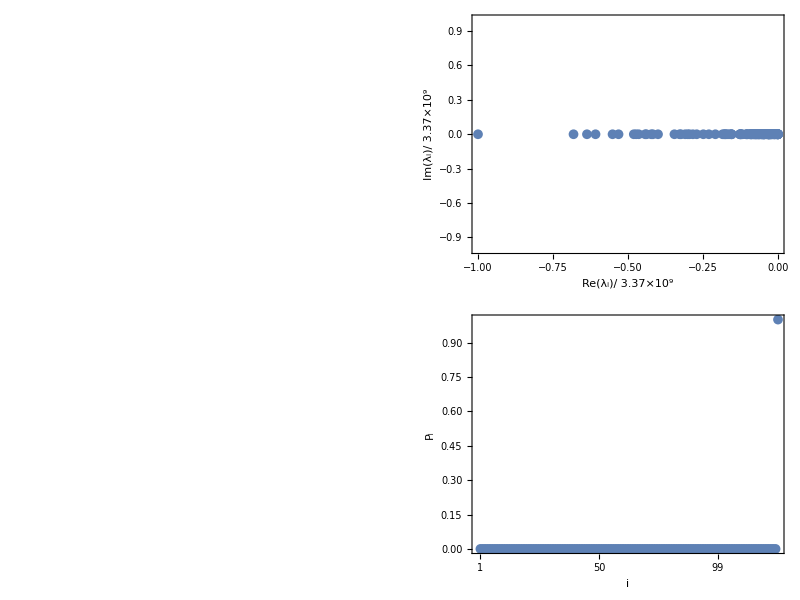

plots/example.pdf

{5 (Ar_1)+4 (O_1 H_2),5 (Ar_1)+H_2+2 (O_1 H_2)+O_2 H_2,5 (Ar_1)+H_1+O_1 H_1+3 (O_1 H_2),5 (Ar_1)+H_2+O_1+3 (O_1 H_2),5 (Ar_1)+2 (H_2)+2 (O_1 H_2)+O_2,5 (Ar_1)+H_2+2 (O_1 H_1)+2 (O_1 H_2),5 (Ar_1)+4 (H_2)+2 (O_2),5 (Ar_1)+2 (H_2)+2 (O_2 H_2),5 (Ar_1)+3 (H_2)+O_2+O_2 H_2,5 (Ar_1)+H_1+H_2+2 (O_1 H_2)+O_2 H_1,5 (Ar_1)+3 (H_2)+2 (O_2 H_1),5 (Ar_1)+8 (H_1)+4 (O_1),5 (Ar_1)+3 (H_2)+O_1+O_1 H_2+O_2,5 (Ar_1)+3 (H_2)+2 (O_1 H_1)+O_2,5 (Ar_1)+2 (H_2)+O_1 H_1+O_1 H_2+O_2 H_1,5 (Ar_1)+H_1+2 (H_2)+O_1 H_1+O_1 H_2+O_2,5 (Ar_1)+H_1+3 (H_2)+O_2+O_2 H_1,5 (Ar_1)+2 (H_2)+2 (O_1 H_1)+O_2 H_2,5 (Ar_1)+H_1+H_2+O_1+O_1 H_1+2 (O_1 H_2),5 (Ar_1)+2 (H_2)+2 (O_1)+2 (O_1 H_2),5 (Ar_1)+2 (H_2)+O_1+O_1 H_2+O_2 H_2,5 (Ar_1)+2 (H_1)+H_2+2 (O_1 H_2)+O_2,5 (Ar_1)+2 (H_2)+O_1+2 (O_1 H_1)+O_1 H_2,5 (Ar_1)+H_1+H_2+O_1 H_1+O_1 H_2+O_2 H_2,5 (Ar_1)+H_1+2 (H_2)+O_2 H_1+O_2 H_2,5 (Ar_1)+8 (H_1)+2 (O_1)+O_2,5 (Ar_1)+6 (H_1)+2 (O_1)+2 (O_1 H_1),5 (Ar_1)+3 (H_2)+O_1+O_1 H_1+O_2 H_1,5 (Ar_1)+3 (H_2)+3 (O_1)+O_1 H_2,5 (Ar_1)+H_1+H_2+3 (O_1 H_1)+O_1 H_2,5 (Ar_1)+6 (H_1)+2 (O_1)+O_2 H_2,5 (Ar_1)+4 (H_1)+2 (H_2)+4 (O_1),5 (Ar_1)+2 (H_1)+2 (O_1 H_2)+O_2 H_2,5 (Ar_1)+2 (H_1)+2 (H_2)+3 (O_1)+O_1 H_2,5 (Ar_1)+5 (H_1)+O_1+3 (O_1 H_1),5 (Ar_1)+2 (H_1)+3 (H_2)+4 (O_1),5 (Ar_1)+5 (H_1)+H_2+3 (O_1)+O_1 H_1,5 (Ar_1)+2 (H_1)+O_1+3 (O_1 H_2),5 (Ar_1)+7 (H_1)+3 (O_1)+O_1 H_1,5 (Ar_1)+H_1+2 (H_2)+2 (O_1)+O_1 H_1+O_1 H_2,5 (Ar_1)+4 (H_2)+4 (O_1),5 (Ar_1)+7 (H_1)+2 (O_1)+O_2 H_1,5 (Ar_1)+2 (H_1)+2 (O_1 H_1)+2 (O_1 H_2),5 (Ar_1)+6 (H_1)+H_2+4 (O_1),5 (Ar_1)+4 (H_2)+2 (O_1)+O_2,5 (Ar_1)+H_1+3 (H_2)+3 (O_1)+O_1 H_1,5 (Ar_1)+2 (H_1)+2 (H_2)+2 (O_1)+O_2 H_2,5 (Ar_1)+7 (H_1)+O_1+O_1 H_1+O_2,5 (Ar_1)+3 (H_1)+2 (H_2)+3 (O_1)+O_1 H_1,5 (Ar_1)+H_1+2 (H_2)+O_1+O_1 H_2+O_2 H_1,5 (Ar_1)+2 (H_1)+3 (H_2)+2 (O_1)+O_2,5 (Ar_1)+4 (H_1)+4 (O_1 H_1),5 (Ar_1)+2 (H_1)+H_2+O_1+2 (O_1 H_1)+O_1 H_2,5 (Ar_1)+H_1+3 (H_2)+O_1+O_1 H_1+O_2,5 (Ar_1)+2 (H_1)+2 (H_2)+O_1+O_1 H_2+O_2,5 (Ar_1)+4 (H_1)+2 (H_2)+2 (O_1)+O_2,5 (Ar_1)+4 (H_1)+H_2+2 (O_1)+2 (O_1 H_1),5 (Ar_1)+5 (H_1)+2 (O_1)+O_1 H_1+O_1 H_2,5 (Ar_1)+2 (H_1)+H_2+O_1+O_1 H_2+O_2 H_2,5 (Ar_1)+2 (H_1)+2 (H_2)+2 (O_1 H_1)+O_2,5 (Ar_1)+4 (H_1)+H_2+3 (O_1)+O_1 H_2,5 (Ar_1)+3 (H_1)+O_1+O_1 H_1+2 (O_1 H_2),5 (Ar_1)+4 (H_1)+H_2+2 (O_1)+O_2 H_2,5 (Ar_1)+3 (H_1)+3 (O_1 H_1)+O_1 H_2,5 (Ar_1)+2 (H_1)+3 (H_2)+2 (O_2),5 (Ar_1)+5 (H_1)+H_2+O_1+O_1 H_1+O_2,5 (Ar_1)+4 (H_1)+H_2+2 (O_1 H_1)+O_2,5 (Ar_1)+2 (H_1)+2 (H_2)+O_1+O_1 H_1+O_2 H_1,5 (Ar_1)+H_1+2 (H_2)+O_1+3 (O_1 H_1),5 (Ar_1)+2 (H_1)+2 (H_2)+2 (O_1)+2 (O_1 H_1),5 (Ar_1)+6 (H_1)+O_1+O_1 H_1+O_2 H_1,5 (Ar_1)+3 (H_2)+2 (O_1)+O_2 H_2,5 (Ar_1)+3 (H_1)+H_2+2 (O_1)+O_1 H_1+O_1 H_2,5 (Ar_1)+3 (H_1)+2 (H_2)+2 (O_1)+O_2 H_1,5 (Ar_1)+2 (H_1)+H_2+2 (O_1)+2 (O_1 H_2),5 (Ar_1)+2 (H_1)+H_2+4 (O_1 H_1),5 (Ar_1)+H_1+3 (H_2)+2 (O_1)+O_2 H_1,5 (Ar_1)+H_1+2 (H_2)+2 (O_1 H_1)+O_2 H_1,5 (Ar_1)+4 (H_1)+H_2+O_1+O_1 H_2+O_2,5 (Ar_1)+3 (H_2)+2 (O_1)+2 (O_1 H_1),5 (Ar_1)+3 (H_1)+2 (H_2)+O_1+O_1 H_1+O_2,5 (Ar_1)+2 (H_1)+H_2+2 (O_2 H_2),5 (Ar_1)+5 (H_1)+H_2+2 (O_1)+O_2 H_1,5 (Ar_1)+7 (H_1)+O_2+O_2 H_1,5 (Ar_1)+4 (H_1)+H_2+2 (O_2 H_1),5 (Ar_1)+4 (H_1)+2 (H_2)+2 (O_2),5 (Ar_1)+6 (H_1)+O_1+O_1 H_2+O_2,5 (Ar_1)+4 (H_1)+O_1+O_1 H_2+O_2 H_2,5 (Ar_1)+4 (H_1)+O_1+2 (O_1 H_1)+O_1 H_2,5 (Ar_1)+2 (H_2)+4 (O_1 H_1),5 (Ar_1)+3 (H_1)+H_2+O_1+O_1 H_1+O_2 H_2,5 (Ar_1)+4 (H_1)+H_2+O_2+O_2 H_2,5 (Ar_1)+3 (H_1)+O_1 H_1+O_1 H_2+O_2 H_2,5 (Ar_1)+2 (H_1)+2 (H_2)+O_2+O_2 H_2,5 (Ar_1)+4 (H_1)+2 (O_1 H_1)+O_2 H_2,5 (Ar_1)+6 (H_1)+3 (O_1)+O_1 H_2,5 (Ar_1)+3 (H_1)+H_2+O_1 H_1+O_1 H_2+O_2,5 (Ar_1)+8 (H_1)+2 (O_2),5 (Ar_1)+6 (H_1)+H_2+2 (O_1)+O_2,5 (Ar_1)+3 (H_1)+H_2+O_1+3 (O_1 H_1),5 (Ar_1)+3 (H_1)+H_2+O_1+O_1 H_2+O_2 H_1,5 (Ar_1)+3 (H_1)+H_2+2 (O_1 H_1)+O_2 H_1,5 (Ar_1)+2 (H_1)+2 (H_2)+2 (O_2 H_1),5 (Ar_1)+5 (H_1)+O_1 H_1+O_1 H_2+O_2,5 (Ar_1)+6 (H_1)+H_2+2 (O_2),5 (Ar_1)+H_1+2 (H_2)+O_1+O_1 H_1+O_2 H_2,5 (Ar_1)+2 (H_1)+H_2+O_1 H_1+O_1 H_2+O_2 H_1,5 (Ar_1)+3 (H_1)+2 (O_1 H_2)+O_2 H_1,5 (Ar_1)+3 (H_1)+H_2+O_2 H_1+O_2 H_2,5 (Ar_1)+4 (H_1)+O_1 H_1+O_1 H_2+O_2 H_1,5 (Ar_1)+2 (H_1)+H_2+2 (O_1 H_1)+O_2 H_2,5 (Ar_1)+5 (H_1)+O_1+O_1 H_2+O_2 H_1,5 (Ar_1)+5 (H_1)+H_2+O_2+O_2 H_1,5 (Ar_1)+4 (H_1)+2 (O_2 H_2),5 (Ar_1)+6 (H_1)+2 (O_2 H_1),5 (Ar_1)+4 (H_1)+2 (O_1 H_2)+O_2,5 (Ar_1)+5 (H_1)+2 (O_1 H_1)+O_2 H_1,5 (Ar_1)+6 (H_1)+O_2+O_2 H_2,5 (Ar_1)+5 (H_1)+O_1+O_1 H_1+O_2 H_2,5 (Ar_1)+5 (H_1)+O_2 H_1+O_2 H_2,5 (Ar_1)+6 (H_1)+2 (O_1 H_1)+O_2,5 (Ar_1)+4 (H_1)+H_2+O_1+O_1 H_1+O_2 H_1,5 (Ar_1)+4 (H_1)+2 (O_1)+2 (O_1 H_2),5 (Ar_1)+3 (H_1)+2 (H_2)+O_2+O_2 H_1}

```mathematica
p=Grid[{{rasterizeBackground[MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListPlot[{Re[#]/Max[Abs[evals]],Im[#]/Max[Abs[evals]]}&/@evals,ImageSize->350,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{DisplayForm[RowBox[{Im[Subscript[λ,i]],"/",PaddedForm[Max[Abs[evals]],3]}]],None},{DisplayForm[RowBox[{Re[Subscript[λ,i]],"/",PaddedForm[Max[Abs[evals]],3]}]],Eigenvalues}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]},{rasterizeBackground[MatrixPlot[Reverse[evecs],ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Left eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListPlot[Abs[evecs[[-1]]],ImageSize->350,PlotRange->All,Axes->False,Frame->True,FrameLabel->{{Subscript[P,i],None},{i,"Steady distribution"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]}}]
Export["plots/example.pdf",p]
multiforms[[Reverse[Ordering[Abs[evecs[[-1]]]]]]]
```

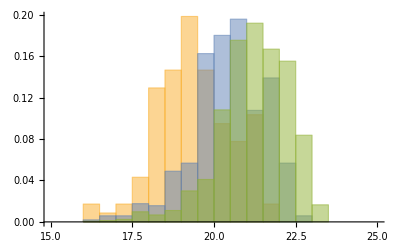

```mathematica
Histogram[{Log[Abs[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList["data/h2o20"<>"eigenvalues.npy","Real64"][[17;;-1]],2]]],Log[Abs[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList["data/h2o21"<>"eigenvalues.npy","Real64"][[17;;-1]],2]]],Log[Abs[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList["data/h2o22"<>"eigenvalues.npy","Real64"][[17;;-1]],2]]]}, {15,25,0.5},"Probability"]
```

## Runtimes

{{9,19,0.0115093,332,9},{12,48,0.0813439,1225,12},{15,89,0.596218,3588,15},{18,177,4.28785,9583,18},{21,298,24.6733,22616,21},{24,516,133.293,50049,24},{27,807,644.169,102480,27}}

{{9,19,0.00166631,332,9},{12,48,0.00269243,1225,12},{15,89,0.0115599,3588,15},{18,177,0.0219312,9583,18},{21,298,0.0630814,22616,21},{24,516,0.150859,50049,24},{27,807,0.324891,102480,27},{30,1277,0.721812,200145,30},{33,1888,1.35229,370476,33},{36,2803,2.49359,661388,36},{39,3965,4.5473,1135106,39},{42,5612,7.90772,1893255,42},{45,7663,12.9912,3063616,45},{48,10450,21.2463,4844184,48},{51,13862,32.9121,7477740,51},{54,18348,51.2392,11324874,54},{57,23760,78.78,16818920,57},{60,30688,113.308,24581466,60}}

{{9,19,0,83,3},{12,48,0,245,4},{15,89,0,598,5},{18,177,1,1369,6},{21,298,2,2827,7},{24,516,1,5561,8},{27,807,2,10248,9},{30,1277,3,18195,10},{33,1888,4,30873,11},{36,2803,3,50876,12},{39,3965,5,81079,13},{42,5612,6,126217,14},{45,7663,6,191476,15},{48,10450,7,284952,16},{51,13862,8,415430,17},{54,18348,9,596046,18},{57,23760,10,840946,19},{60,30688,10,1170546,20},{63,38940,12,1606694,21},{66,49274,13,2180000,22},{69,61446,14,2923048,23},{72,76411,15,3880353,24},{75,93864,17,5099087,25},{78,114989,18,6642312,26},{81,139411,20,8576593,27},{84,168576,21,10989255,28},{87,202029,23,13972160,29},{90,241515,26,17643841,30},{93,286488,28,22128615,31},{96,339030,30,27584561,32},{99,398493,32,34177030,33},{102,467337,35,42113553,34},{105,544800,38,51610691,35},{108,633763,41,62937086,36},{111,733337,45,76372469,37},{114,846870,49,92260201,38},{117,973333,54,110957124,39},{120,1116588,59,132897080,40}}

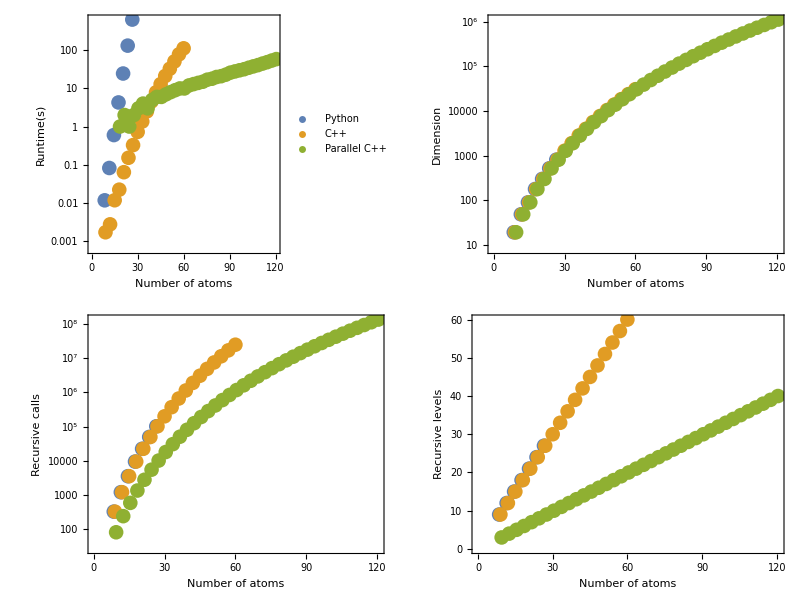

plots/runtimes.pdf

```mathematica
dat=Import["data/runtimesout.dat"]
dat2=Import["data/runtimes2out.dat"]
dat3=Import["data/runtimes3out.dat"]
p=Legended[Grid[{{ListLogPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,3}]],{#[[1]]+0.0,#[[2]]}&/@dat2[[All,{1,3}]],{#[[1]]+0.5,#[[2]]}&/@dat3[[All,{1,3}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Runtime(s)"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]],ListLogPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,2}]],{#[[1]]+0.0,#[[2]]}&/@dat2[[All,{1,2}]],{#[[1]]+0.5,#[[2]]}&/@dat3[[All,{1,2}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Dimension"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]]},{ListLogPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,4}]],{#[[1]]+0.0,#[[2]]}&/@dat2[[All,{1,4}]],{#[[1]]+0.5,#[[2]]}&/@dat3[[All,{1,4}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive calls"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]],ListPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,5}]],{#[[1]]+0.0,#[[2]]}&/@dat2[[All,{1,5}]],{#[[1]]+0.5,#[[2]]}&/@dat3[[All,{1,5}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive levels"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]]}}],Placed[PointLegend[ColorData[97,"ColorList"][[1;;3]],{"Python","C++","Parallel C++"},LegendMarkerSize->20],Right]]
Export["plots/runtimes.pdf",p]
```

## Temperature - pressure sweep

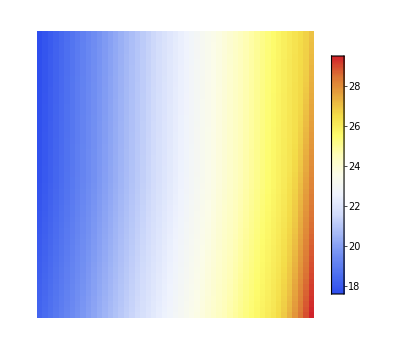
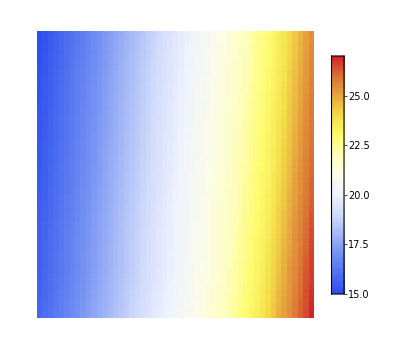
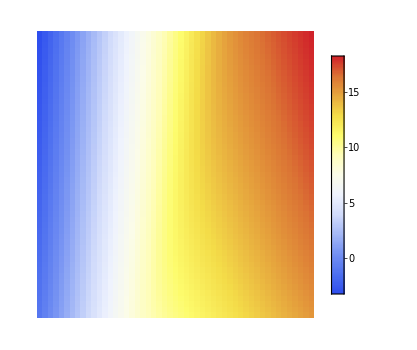
-Graphics- | -Graphics- | -Graphics-

plots/sweep.pdf

```mathematica
press0=0.01;
press1=100.0;
temp0=600;
temp1=1000;
ntemp=50;
npres=50;
sweep=Import["data/sweepout.dat"];
p=Grid[{{ArrayPlot[Transpose[Partition[Log[Abs[Min[#[[4;;-2]]]]]&/@sweep,ntemp+1]],DataReversed->{True,False},ColorFunction->"TemperatureMap",ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Temperature (k)",Log[-Subscript[λ,-1]]},{"Log Pressure/(1atm)",None}},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i+1,Log[press0*(press1/press0)^(i/npres)]/Log[10]},{i,0,npres,npres/5}],None},{Table[{i+1,temp0+(temp1-temp0)*i/ntemp},{i,0,ntemp,ntemp/5}],None}},PlotLegends->True],ArrayPlot[Transpose[Partition[Log[Abs[Median[#[[4;;-2]]]]]&/@sweep,ntemp+1]],DataReversed->{True,False},ColorFunction->"TemperatureMap",ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Temperature (k)",Log[-OverBar[λ]]},{"Log Pressure/(1atm)",None}},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i+1,Log[press0*(press1/press0)^(i/npres)]/Log[10]},{i,0,npres,npres/5}],None},{Table[{i+1,temp0+(temp1-temp0)*i/ntemp},{i,0,ntemp,ntemp/5}],None}},PlotLegends->True],ArrayPlot[Transpose[Partition[Log[Abs[Max[#[[4;;-7]]]]]&/@sweep,ntemp+1]],DataReversed->{True,False},ColorFunction->"TemperatureMap",ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Temperature (k)",Log[-Subscript[λ,1]]},{"Log Pressure/(1atm)",None}},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i+1,Log[press0*(press1/press0)^(i/npres)]/Log[10]},{i,0,npres,npres/5}],None},{Table[{i+1,temp0+(temp1-temp0)*i/ntemp},{i,0,ntemp,ntemp/5}],None}},PlotLegends->True]}}]
Export["plots/sweep.pdf",p]
```

```mathematica
press0*(press1/press0)^(npres/npres)
```

10.

```mathematica
sweep[[1]]
```

{600.,0.01,2.10995,-8.56986×10^7,-8.49482×10^7,-6.39554×10^7,-5.68362×10^7,-5.23651×10^7,-4.72634×10^7,-4.30498×10^7,-4.10387×10^7,-3.94891×10^7,-3.68344×10^7,-3.58209×10^7,-3.33741×10^7,-3.28309×10^7,-3.22756×10^7,-3.21681×10^7,-3.09657×10^7,-3.08022×10^7,-3.06066×10^7,-2.94439×10^7,-2.89851×10^7,-2.70379×10^7,-2.67806×10^7,-2.45407×10^7,-2.44007×10^7,-2.38361×10^7,-2.00244×10^7,-1.95179×10^7,-1.86353×10^7,-1.85501×10^7,-1.84755×10^7,-1.81288×10^7,-1.79913×10^7,-1.78981×10^7,-1.74584×10^7,-1.6571×10^7,-1.50889×10^7,-1.39673×10^7,-1.39016×10^7,-1.24547×10^7,-1.13567×10^7,-1.10916×10^7,-1.09841×10^7,-1.07804×10^7,-8.82913×10^6,-8.73849×10^6,-8.6616×10^6,-8.61266×10^6,-8.48781×10^6,-8.41589×10^6,-8.20774×10^6,-7.90257×10^6,-7.44114×10^6,-7.41873×10^6,-7.40016×10^6,-7.34507×10^6,-6.90292×10^6,-6.14998×10^6,-6.08533×10^6,-5.90071×10^6,-5.76306×10^6,-5.73511×10^6,-5.60781×10^6,-5.54548×10^6,-5.24033×10^6,-4.87368×10^6,-4.76722×10^6,-4.73039×10^6,-4.72556×10^6,-4.3716×10^6,-4.3509×10^6,-4.30352×10^6,-3.93801×10^6,-3.92727×10^6,-3.62924×10^6,-3.59886×10^6,-3.54959×10^6,-3.53057×10^6,-3.43767×10^6,-3.26336×10^6,-3.1631×10^6,-3.15248×10^6,-3.12666×10^6,-3.08061×10^6,-2.50045×10^6,-2.26422×10^6,-2.10834×10^6,-2.05682×10^6,-1.73908×10^6,-1.51911×10^6,-1.33188×10^6,-1.20724×10^6,-1.11381×10^6,-1.05424×10^6,-894958.,-807825.,-792475.,-687149.,-616617.,-476607.,-437594.,-409723.,-372869.,-294612.,-237350.,-209378.,-157765.,-145393.,-71492.4,-19002.6,-9060.55,-6968.77,-3920.42,-3484.07,-1742.5,-1442.96,-1307.01,-1.35393,-0.32795,-1.8663×10^-9,-9.42765×10^-10,-4.14389×10^-10,-4.14389×10^-10,-1.96721×10^-10,-1.82134×10^-43}

```mathematica
Max[#[[4;;-7]]]&/@sweep
```

{-0.32795,-0.311547,-0.296077,-0.28148,-0.267705,-0.254699,-0.242417,-0.230813,-0.219847,-0.20948,-0.199675,-0.1904,-0.181622,-0.173311,-0.16544,-0.157983,-0.150915,-0.144214,-0.137859,-0.131829,-0.126105,-0.120671,-0.11551,-0.110606,-0.105945,-0.101514,-0.0972987,-0.0932883,-0.0894713,-0.0858372,-0.082376,-0.0790785,-0.0759359,-0.0729398,-0.0700827,-0.0673571,-0.0647563,-0.0622736,-0.0599031,-0.0576389,-0.0554757,-0.0534083,-0.0514319,-0.0495419,-0.0477341,-0.0460044,-0.0443489,-0.0427641,-0.0412465,-0.0397928,-0.0384001,-0.569778,-0.541298,-0.514433,-0.489083,-0.465156,-0.442566,-0.42123,-0.401072,-0.382021,-0.36401,-0.346976,-0.33086,-0.315608,-0.301167,-0.287491,-0.274534,-0.262253,-0.250609,-0.239565,-0.229087,-0.219142,-0.209699,-0.20073,-0.192209,-0.184109,-0.176408,-0.169084,-0.162114,-0.155481,-0.149166,-0.143151,-0.137421,-0.13196,-0.126754,-0.121788,-0.117052,-0.112532,-0.108218,-0.104098,-0.100164,-0.0964043,-0.0928115,-0.0893769,-0.0860924,-0.0829508,-0.0799448,-0.0770678,-0.0743136,-0.0716761,-0.0691497,-0.0667292,-0.989825,-0.940394,-0.893757,-0.849744,-0.808197,-0.768965,-0.731909,-0.696896,-0.663804,-0.632516,-0.602924,-0.574926,-0.548427,-0.523338,-0.499576,-0.477062,-0.455724,-0.435492,-0.416303,-0.398096,-0.380815,-0.364406,-0.348821,-0.334014,-0.319939,-0.306557,-0.293828,-0.281718,-0.270192,-0.259217,-0.248765,-0.238807,-0.229317,-0.220269,-0.211641,-0.20341,-0.195556,-0.188058,-0.180899,-0.174062,-0.167529,-0.161285,-0.155316,-0.149609,-0.144149,-0.138925,-0.133925,-0.129139,-0.124555,-0.120165,-0.115958,-1.71928,-1.63353,-1.55261,-1.47622,-1.4041,-1.33599,-1.27165,-1.21085,-1.15338,-1.09903,-1.04763,-0.998999,-0.952966,-0.909381,-0.868099,-0.828984,-0.79191,-0.756758,-0.723417,-0.691781,-0.661754,-0.633243,-0.606163,-0.580432,-0.555975,-0.532721,-0.510603,-0.489559,-0.46953,-0.450459,-0.432296,-0.414992,-0.3985,-0.382778,-0.367784,-0.35348,-0.339831,-0.326802,-0.314362,-0.302479,-0.291126,-0.280276,-0.269904,-0.259985,-0.250497,-0.241419,-0.23273,-0.224412,-0.216446,-0.208816,-0.201505,-2.98565,-2.83702,-2.6967,-2.56421,-2.43909,-2.32089,-2.20921,-2.10366,-2.00388,-1.90952,-1.82026,-1.73579,-1.65584,-1.58013,-1.50842,-1.44047,-1.37606,-1.31499,-1.25707,-1.2021,-1.14993,-1.1004,-1.05334,-1.00863,-0.966137,-0.925731,-0.887299,-0.850731,-0.815926,-0.782788,-0.751227,-0.721157,-0.692498,-0.665177,-0.639122,-0.614266,-0.590547,-0.567906,-0.546287,-0.525638,-0.505909,-0.487054,-0.469029,-0.451792,-0.435303,-0.419527,-0.404428,-0.389972,-0.376129,-0.362869,-0.350165,-5.18317,-4.92585,-4.68278,-4.45316,-4.23623,-4.03124,-3.83751,-3.65437,-3.48119,-3.3174,-3.16243,-3.01578,-2.87694,-2.74547,-2.62092,-2.5029,-2.39103,-2.28495,-2.18432,-2.08883,-1.99819,-1.91213,-1.83038,-1.7527,-1.67886,-1.60866,-1.54188,-1.47834,-1.41786,-1.36028,-1.30544,-1.25319,-1.20339,-1.15591,-1.11064,-1.06744,-1.02623,-0.986882,-0.949314,-0.913431,-0.879147,-0.846382,-0.815058,-0.785103,-0.75645,-0.729034,-0.702794,-0.677674,-0.653617,-0.630574,-0.608495,-8.99404,-8.54927,-8.12881,-7.73136,-7.35566,-7.00048,-6.66466,-6.34709,-6.04673,-5.76256,-5.49366,-5.23912,-4.99812,-4.76987,-4.55362,-4.34868,-4.1544,-3.97015,-3.79537,-3.62951,-3.47207,-3.32256,-3.18054,-3.04559,-2.91731,-2.79533,-2.67931,-2.56891,-2.46383,-2.36378,-2.26849,-2.1777,-2.09117,-2.00867,-1.92999,-1.85494,-1.78332,-1.71495,-1.64967,-1.58731,-1.52774,-1.4708,-1.41637,-1.36431,-1.31452,-1.26688,-1.22128,-1.17762,-1.13582,-1.09577,-1.0574,-15.5966,-14.8297,-14.1039,-13.4171,-12.7675,-12.1528,-11.5714,-11.0213,-10.5008,-10.0081,-9.5418,-9.10028,-8.68214,-8.28605,-7.91072,-7.55496,-7.21766,-6.89776,-6.59425,-6.30622,-6.03277,-5.7731,-5.52641,-5.29199,-5.06915,-4.85725,-4.65569,-4.46389,-4.28133,-4.1075,-3.94193,-3.78418,-3.63383,-3.49049,-3.35378,-3.22337,-3.09892,-2.98012,-2.86668,-2.75833,-2.6548,-2.55586,-2.46127,-2.37081,-2.28429,-2.2015,-2.12226,-2.04639,-1.97375,-1.90416,-1.83748,-27.0203,-25.7027,-24.4536,-23.2701,-22.1491,-21.0876,-20.0826,-19.131,-18.23,-17.3769,-16.569,-15.8038,-15.0788,-14.3919,-13.7408,-13.1236,-12.5382,-11.983,-11.4561,-10.9561,-10.4813,-10.0304,-9.60197,-9.19485,-8.80781,-8.43975,-8.08962,-7.75645,-7.4393,-7.13732,-6.84968,-6.57561,-6.31439,-6.06534,-5.82782,-5.60123,-5.38499,-5.17856,-4.98145,-4.79318,-4.61329,-4.44136,-4.277,-4.11982,-3.96946,-3.82559,-3.68789,-3.55607,-3.42982,-3.30889,-3.19302,-46.7475,-44.4952,-42.355,-40.323,-38.3952,-36.5669,-34.8338,-33.1911,-31.6345,-30.1594,-28.7616,-27.4369,-26.1813,-24.9911,-23.8626,-22.7924,-21.7773,-20.8141,-19.9,-19.0322,-18.2082,-17.4255,-16.6817,-15.9749,-15.3028,-14.6636,-14.0556,-13.4769,-12.9261,-12.4015,-11.9019,-11.4258,-10.972,-10.5393,-10.1267,-9.73298,-9.35728,-8.99863,-8.65616,-8.32903,-8.01646,-7.71773,-7.43213,-7.159,-6.89774,-6.64775,-6.40847,-6.1794,-5.96002,-5.74988,-5.54853,-80.7173,-76.8968,-73.2533,-69.7838,-66.4837,-63.3476,-60.3694,-57.5424,-54.86,-52.3153,-49.9017,-47.6124,-45.4412,-43.3817,-41.428,-39.5744,-37.8154,-36.146,-34.5611,-33.0561,-31.6267,-30.2687,-28.9781,-27.7513,-26.5847,-25.4751,-24.4194,-23.4146,-22.4581,-21.5471,-20.6794,-19.8524,-19.0642,-18.3127,-17.5959,-16.912,-16.2593,-15.6362,-15.0412,-14.4729,-13.9298,-13.4108,-12.9145,-12.44,-11.986,-11.5516,-11.1359,-10.7378,-10.3566,-9.99148,-9.6416,-138.975,-132.567,-126.423,-120.547,-114.937,-109.589,-104.498,-99.6538,-95.049,-90.6738,-86.518,-82.5719,-78.8253,-75.2685,-71.8919,-68.6862,-65.6425,-62.7522,-60.0072,-57.3996,-54.9221,-52.5676,-50.3295,-48.2015,-46.1776,-44.2522,-42.4201,-40.6761,-39.0156,-37.4341,-35.9274,-34.4915,-33.1227,-31.8175,-30.5726,-29.3847,-28.251,-27.1687,-26.1351,-25.1478,-24.2044,-23.3027,-22.4405,-21.6161,-20.8273,-20.0726,-19.3502,-18.6586,-17.9963,-17.3618,-16.7538,-238.302,-227.732,-217.518,-207.684,-198.245,-189.206,-180.566,-172.32,-164.459,-156.972,-149.847,-143.07,-136.626,-130.5,-124.679,-119.147,-113.89,-108.895,-104.147,-99.6352,-95.3462,-91.2684,-87.3908,-83.7027,-80.1941,-76.8554,-73.6777,-70.6523,-67.7711,-65.0267,-62.4116,-59.9192,-57.543,-55.277,-53.1153,-51.0527,-49.0839,-47.2043,-45.4091,-43.6943,-42.0555,-40.4892,-38.9916,-37.5593,-36.1891,-34.8779,-33.6229,-32.4213,-31.2705,-30.1681,-29.1118,-406.218,-389.225,-372.603,-356.441,-340.799,-325.717,-311.218,-297.313,-284.004,-271.285,-259.144,-247.567,-236.535,-226.029,-216.029,-206.512,-197.458,-188.846,-180.653,-172.861,-165.448,-158.397,-151.688,-145.304,-139.228,-133.444,-127.937,-122.693,-117.697,-112.938,-108.402,-104.078,-99.9545,-96.0218,-92.2699,-88.6895,-85.2716,-82.0082,-78.8912,-75.9133,-73.0675,-70.3473,-67.7462,-65.2585,-62.8784,-60.6009,-58.4207,-56.3333,-54.3342,-52.419,-50.5838,-686.655,-660.4,-634.229,-608.386,-583.058,-558.38,-534.452,-511.337,-489.077,-467.694,-447.194,-427.573,-408.816,-390.906,-373.816,-357.521,-341.991,-327.195,-313.103,-299.682,-286.904,-274.737,-263.152,-252.12,-241.615,-231.609,-222.079,-212.998,-204.346,-196.099,-188.237,-180.741,-173.592,-166.771,-160.262,-154.05,-148.12,-142.456,-137.046,-131.877,-126.936,-122.213,-117.697,-113.377,-109.244,-105.288,-101.502,-97.8763,-94.4038,-91.077,-87.8891,-1146.95,-1108.93,-1069.83,-1030.25,-990.683,-951.5,-912.994,-875.386,-838.832,-803.446,-769.298,-736.431,-704.865,-674.6,-645.623,-617.909,-591.429,-566.144,-542.014,-518.997,-497.048,-476.122,-456.174,-437.161,-419.039,-401.766,-385.301,-369.605,-354.64,-340.37,-326.761,-313.78,-301.394,-289.575,-278.294,-267.524,-257.24,-247.416,-238.031,-229.062,-220.49,-212.293,-204.454,-196.955,-189.78,-182.912,-176.338,-170.042,-164.012,-158.234,-152.698,-1884.24,-1835.12,-1781.66,-1725.19,-1666.82,-1607.48,-1547.92,-1488.73,-1430.36,-1373.18,-1317.45,-1263.36,-1211.04,-1160.57,-1112.,-1065.34,-1020.58,-977.706,-936.671,-897.431,-859.93,-824.11,-789.908,-757.26,-726.103,-696.372,-668.004,-640.937,-615.111,-590.467,-566.95,-544.505,-523.08,-502.626,-483.095,-464.443,-446.626,-429.603,-413.335,-397.785,-382.919,-368.702,-355.104,-342.093,-329.643,-317.724,-306.313,-295.385,-284.917,-274.886,-265.273,-3026.47,-2976.46,-2914.73,-2843.75,-2765.75,-2682.7,-2596.28,-2507.9,-2418.74,-2329.72,-2241.59,-2154.94,-2070.19,-1987.69,-1907.67,-1830.28,-1755.62,-1683.74,-1614.66,-1548.36,-1484.79,-1423.9,-1365.61,-1309.86,-1256.56,-1205.61,-1156.92,-1110.41,-1065.98,-1023.54,-983.002,-944.283,-907.299,-871.967,-838.212,-805.958,-775.134,-745.672,-717.507,-690.576,-664.821,-640.184,-616.614,-594.057,-572.467,-551.796,-532.002,-513.042,-494.877,-477.47,-460.786,-4720.74,-4700.72,-4655.12,-4587.56,-4501.72,-4401.12,-4289.03,-4168.37,-4041.69,-3911.16,-3778.61,-3645.52,-3513.11,-3382.32,-3253.92,-3128.46,-3006.36,-2887.94,-2773.38,-2662.82,-2556.31,-2453.87,-2355.46,-2261.02,-2170.48,-2083.72,-2000.64,-1921.13,-1845.04,-1772.26,-1702.65,-1636.08,-1572.43,-1511.56,-1453.37,-1397.72,-1344.5,-1293.6,-1244.92,-1198.35,-1153.79,-1111.15,-1070.34,-1031.28,-993.877,-958.058,-923.749,-890.88,-859.383,-829.195,-800.254,-7105.63,-7179.93,-7208.22,-7193.74,-7140.74,-7054.02,-6938.64,-6799.6,-6641.62,-6469.04,-6285.7,-6094.96,-5899.66,-5702.18,-5504.49,-5308.18,-5114.52,-4924.49,-4738.84,-4558.15,-4382.82,-4213.11,-4049.19,-3891.14,-3738.98,-3592.66,-3452.09,-3317.17,-3187.76,-3063.69,-2944.8,-2830.92,-2721.85,-2617.43,-2517.45,-2421.75,-2330.14,-2242.46,-2158.52,-2078.16,-2001.23,-1927.58,-1857.04,-1789.49,-1724.79,-1662.8,-1603.4,-1546.48,-1491.92,-1439.62,-1389.46,-10279.5,-10551.3,-10755.8,-10892.1,-10961.9,-10968.7,-10917.5,-10814.7,-10667.,-10481.2,-10264.2,-10022.4,-9761.44,-9486.51,-9202.07,-8911.92,-8619.25,-8326.7,-8036.42,-7750.12,-7469.15,-7194.56,-6927.11,-6667.39,-6415.75,-6172.46,-5937.62,-5711.27,-5493.35,-5283.76,-5082.34,-4888.91,-4703.25,-4525.13,-4354.3,-4190.51,-4033.5,-3883.02,-3738.81,-3600.61,-3468.19,-3341.29,-3219.68,-3103.13,-2991.43,-2884.35,-2781.71,-2683.29,-2588.92,-2498.41,-2411.59,-14291.4,-14892.5,-15415.2,-15850.9,-16193.6,-16440.7,-16592.5,-16652.3,-16625.8,-16520.4,-16344.9,-16108.7,-15821.2,-15491.5,-15128.2,-14739.1,-14331.1,-13910.3,-13481.8,-13049.9,-12618.4,-12190.1,-11767.5,-11352.5,-10946.5,-10550.6,-10165.7,-9792.35,-9430.91,-9081.58,-8744.42,-8419.41,-8106.4,-7805.21,-7515.58,-7237.23,-6969.86,-6713.11,-6466.64,-6230.1,-6003.13,-5785.36,-5576.45,-5376.03,-5183.77,-4999.32,-4822.38,-4652.61,-4489.72,-4333.41,-4183.4,-19169.1,-20238.6,-21239.6,-22154.4,-22967.1,-23664.3,-24235.8,-24675.3,-24980.5,-25153.1,-25198.6,-25125.1,-24943.4,-24665.4,-24303.9,-23871.7,-23381.2,-22844.1,-22270.8,-21670.8,-21052.6,-20423.2,-19788.6,-19154.,-18523.6,-17900.8,-17288.4,-16688.4,-16102.5,-15532.1,-14977.9,-14440.6,-13920.5,-13417.8,-12932.5,-12464.4,-12013.4,-11579.1,-11161.1,-10759.1,-10372.5,-10001.,-9644.01,-9301.02,-8971.56,-8655.13,-8351.23,-8059.37,-7779.09,-7509.91,-7251.39,-24962.2,-26631.7,-28266.6,-29843.2,-31337.2,-32724.7,-33982.9,-35091.8,-36034.6,-36799.2,-37378.4,-37770.3,-37978.1,-38009.6,-37876.3,-37592.8,-37175.2,-36640.9,-36007.1,-35290.7,-34507.6,-33672.2,-32797.8,-31895.8,-30976.4,-30048.,-29118.1,-28192.7,-27276.7,-26374.2,-25488.5,-24622.,-23776.7,-22954.1,-22155.2,-21380.5,-20630.4,-19905.1,-19204.5,-18528.4,-17876.3,-17247.9,-16642.6,-16059.8,-15498.9,-14959.2,-14440.1,-13940.9,-13460.8,-12999.2,-12555.4,-31772.7,-34165.4,-36578.3,-38986.3,-41361.4,-43673.7,-45891.5,-47982.7,-49916.,-51662.1,-53195.3,-54494.3,-55543.9,-56335.3,-56866.6,-57142.1,-57172.4,-56972.7,-56562.3,-55962.9,-55197.5,-54289.6,-53262.,-52136.5,-50933.2,-49670.4,-48364.4,-47029.6,-45678.3,-44321.1,-42967.,-41623.4,-40296.3,-38990.8,-37710.9,-36459.5,-35239.,-34051.3,-32897.3,-31778.,-30693.7,-29644.5,-28630.1,-27650.4,-26704.7,-25792.4,-24912.7,-24065.,-23248.2,-22461.4,-21703.8,-39766.7,-43006.1,-46336.8,-49736.,-53177.1,-56629.4,-60058.7,-63427.3,-66695.,-69820.1,-72760.5,-75475.2,-77926.1,-80079.5,-81907.9,-83391.2,-84517.4,-85283.3,-85694.1,-85762.6,-85508.3,-84956.,-84133.9,-83072.7,-81803.8,-80358.2,-78765.7,-77054.4,-75250.,-73375.7,-71452.,-69497.1,-67526.6,-65553.8,-63589.9,-61644.3,-59724.9,-57837.8,-55988.,-54179.5,-52415.4,-50697.6,-49027.9,-47407.1,-45835.7,-44313.7,-42841.1,-41417.2,-40041.4,-38712.8,-37430.3,-49174.7,-53396.5,-57793.4,-62347.8,-67037.7,-71836.2,-76711.9,-81628.2,-86543.6,-91412.2,-96184.3,-100807.,-105225.,-109383.,-113229.,-116711.,-119786.,-122416.,-124573.,-126239.,-127409.,-128086.,-128285.,-128029.,-127349.,-126281.,-124865.,-123141.,-121154.,-118942.,-116545.,-113999.,-111338.,-108591.,-105785.,-102943.,-100085.,-97229.,-94388.6,-91576.4,-88802.5,-86075.2,-83401.1,-80785.3,-78231.9,-75743.9,-73323.2,-70971.2,-68688.7,-66475.7,-64332.,-60292.3,-65655.1,-71288.6,-77181.9,-83319.5,-89681.3,-96242.1,-102971.,-109832.,-116781.,-123770.,-130745.,-137645.,-144404.,-150954.,-157224.,-163141.,-168635.,-173641.,-178097.,-181953.,-185169.,-187718.,-189585.,-190771.,-191290.,-191168.,-190440.,-189151.,-187352.,-185097.,-182441.,-179439.,-176147.,-172613.,-168887.,-165010.,-161023.,-156960.,-152852.,-148725.,-144602.,-140503.,-136443.,-132437.,-128496.,-124628.,-120842.,-117142.,-113533.,-110018.,-73484.,-80179.,-87253.1,-94702.6,-102520.,-110693.,-119205.,-128034.,-137151.,-146522.,-156105.,-165852.,-175706.,-185605.,-195475.,-205241.,-214817.,-224115.,-233043.,-241507.,-249414.,-256677.,-263215.,-268956.,-273842.,-277828.,-280890.,-283017.,-284217.,-284516.,-283952.,-282577.,-280453.,-277648.,-274234.,-270286.,-265875.,-261074.,-255949.,-250563.,-244974.,-239234.,-233388.,-227479.,-221541.,-215607.,-209702.,-203850.,-198069.,-192375.,-186781.,-89191.1,-97451.5,-106214.,-115484.,-125260.,-135541.,-146319.,-157582.,-169312.,-181484.,-194069.,-207028.,-220316.,-233878.,-247652.,-261564.,-275534.,-289470.,-303275.,-316840.,-330053.,-342795.,-354946.,-366385.,-376995.,-386666.,-395299.,-402807.,-409122.,-414196.,-418001.,-420532.,-421805.,-421857.,-420744.,-418535.,-415312.,-411166.,-406192.,-400487.,-394149.,-387272.,-379944.,-372250.,-364267.,-356064.,-347706.,-339248.,-330740.,-322225.,-313740.,-107944.,-118055.,-128809.,-140220.,-152297.,-165047.,-178473.,-192573.,-207341.,-222765.,-238827.,-255503.,-272760.,-290557.,-308846.,-327567.,-346651.,-366019.,-385579.,-405230.,-424857.,-444337.,-463537.,-482312.,-500513.,-517986.,-534575.,-550126.,-564490.,-577529.,-589119.,-599155.,-607553.,-614255.,-619229.,-622472.,-624008.,-623885.,-622176.,-618971.,-614378.,-608514.,-601503.,-593474.,-584555.,-574869.,-564538.,-553673.,-542379.,-530753.,-518882.,-130381.,-142688.,-155803.,-169748.,-184542.,-200202.,-216742.,-234172.,-252497.,-271719.,-291834.,-312830.,-334691.,-357393.,-380903.,-405179.,-430169.,-455811.,-482031.,-508744.,-535850.,-563238.,-590781.,-618341.,-645764.,-672884.,-699525.,-725499.,-750611.,-774663.,-797453.,-818785.,-838469.,-856331.,-872212.,-885978.,-897523.,-906770.,-913679.,-918241.,-920484.,-920466.,-918277.,-914029.,-907858.,-899913.,-890356.,-879353.,-867071.,-853677.,-839330.,-157263.,-172188.,-188113.,-205070.,-223090.,-242199.,-262423.,-283784.,-306301.,-329989.,-354858.,-380913.,-408152.,-436569.,-466149.,-496869.,-528697.,-561592.,-595501.,-630361.,-666095.,-702613.,-739810.,-777568.,-815749.,-854203.,-892760.,-931236.,-969430.,-1.00712×10^6,-1.04409×10^6,-1.08008×10^6,-1.11485×10^6,-1.14815×10^6,-1.17971×10^6,-1.20928×10^6,-1.23662×10^6,-1.26151×10^6,-1.28374×10^6,-1.30313×10^6,-1.31955×10^6,-1.33288×10^6,-1.34306×10^6,-1.35007×10^6,-1.35393×10^6,-1.3547×10^6,-1.35249×10^6,-1.34743×10^6,-1.33968×10^6,-1.32944×10^6,-1.3169×10^6,-189507.,-207560.,-226840.,-247390.,-269251.,-292464.,-317066.,-343093.,-370577.,-399548.,-430031.,-462047.,-495612.,-530736.,-567424.,-605673.,-645473.,-686803.,-729636.,-773932.,-819639.,-866696.,-915024.,-964533.,-1.01511×10^6,-1.06664×10^6,-1.11898×10^6,-1.17196×10^6,-1.22541×10^6,-1.27912×10^6,-1.33288×10^6,-1.38645×10^6,-1.43956×10^6,-1.49193×10^6,-1.54328×10^6,-1.5933×10^6,-1.64165×10^6,-1.68803×10^6,-1.7321×10^6,-1.77353×10^6,-1.81201×10^6,-1.84726×10^6,-1.87899×10^6,-1.90697×10^6,-1.93101×10^6,-1.95094×10^6,-1.96666×10^6,-1.97812×10^6,-1.98532×10^6,-1.98831×10^6,-1.9872×10^6,-228210.,-250009.,-273302.,-298147.,-324599.,-352710.,-382533.,-414118.,-447513.,-482762.,-519907.,-558987.,-600036.,-643082.,-688151.,-735259.,-784418.,-835633.,-888899.,-944202.,-1.00152×10^6,-1.06081×10^6,-1.12204×10^6,-1.18514×10^6,-1.25004×10^6,-1.31665×10^6,-1.38485×10^6,-1.45453×10^6,-1.52555×10^6,-1.59772×10^6,-1.67088×10^6,-1.7448×10^6,-1.81926×10^6,-1.894×10^6,-1.96874×10^6,-2.04317×10^6,-2.11697×10^6,-2.18977×10^6,-2.26121×10^6,-2.3309×10^6,-2.39844×10^6,-2.4634×10^6,-2.52539×10^6,-2.58396×10^6,-2.63874×10^6,-2.68931×10^6,-2.73534×10^6,-2.77648×10^6,-2.81246×10^6,-2.84305×10^6,-2.86807×10^6,-274691.,-300979.,-329082.,-359071.,-391017.,-424989.,-461054.,-499279.,-539729.,-582465.,-627548.,-675035.,-724979.,-777430.,-832432.,-890027.,-950247.,-1.01312×10^6,-1.07867×10^6,-1.14691×10^6,-1.21784×10^6,-1.29146×10^6,-1.36776×10^6,-1.4467×10^6,-1.52824×10^6,-1.61234×10^6,-1.69892×10^6,-1.78789×10^6,-1.87916×10^6,-1.97261×10^6,-2.06808×10^6,-2.16542×10^6,-2.26444×10^6,-2.36492×10^6,-2.46662×10^6,-2.56929×10^6,-2.67262×10^6,-2.77629×10^6,-2.87995×10^6,-2.98322×10^6,-3.08568×10^6,-3.1869×10^6,-3.28642×10^6,-3.38374×10^6,-3.47836×10^6,-3.56977×10^6,-3.65743×10^6,-3.7408×10^6,-3.81938×10^6,-3.89265×10^6,-3.96013×10^6,-330532.,-362206.,-396078.,-432237.,-470769.,-511763.,-555304.,-601477.,-650367.,-702055.,-756622.,-814146.,-874700.,-938358.,-1.00519×10^6,-1.07525×10^6,-1.14861×10^6,-1.22531×10^6,-1.30541×10^6,-1.38895×10^6,-1.47596×10^6,-1.56647×10^6,-1.66048×10^6,-1.75802×10^6,-1.85907×10^6,-1.96362×10^6,-2.07164×10^6,-2.18309×10^6,-2.2979×10^6,-2.416×10^6,-2.5373×10^6,-2.66168×10^6,-2.789×10^6,-2.91911×10^6,-3.05182×10^6,-3.18692×10^6,-3.32418×10^6,-3.46332×10^6,-3.60406×10^6,-3.74606×10^6,-3.88895×10^6,-4.03233×10^6,-4.17578×10^6,-4.31883×10^6,-4.46096×10^6,-4.60165×10^6,-4.74031×10^6,-4.87635×10^6,-5.00915×10^6,-5.13806×10^6,-5.26241×10^6,-397633.,-435774.,-476572.,-520135.,-566570.,-615987.,-668492.,-724193.,-783197.,-845607.,-911527.,-981059.,-1.0543×10^6,-1.13135×10^6,-1.2123×10^6,-1.29725×10^6,-1.38627×10^6,-1.47944×10^6,-1.57686×10^6,-1.67858×10^6,-1.78467×10^6,-1.89519×10^6,-2.01019×10^6,-2.12971×10^6,-2.25378×10^6,-2.38243×10^6,-2.51566×10^6,-2.65348×10^6,-2.79587×10^6,-2.9428×10^6,-3.09422×10^6,-3.25008×10^6,-3.41029×10^6,-3.57474×10^6,-3.74332×10^6,-3.91587×10^6,-4.09223×10^6,-4.2722×10^6,-4.45553×10^6,-4.64199×10^6,-4.83126×10^6,-5.02304×10^6,-5.21694×10^6,-5.41257×10^6,-5.60949×10^6,-5.80722×10^6,-6.00523×10^6,-6.20296×10^6,-6.39979×10^6,-6.59508×10^6,-6.78813×10^6,-478277.,-524187.,-573303.,-625756.,-681680.,-741207.,-804472.,-871605.,-942740.,-1.01801×10^6,-1.09754×10^6,-1.18146×10^6,-1.2699×10^6,-1.36299×10^6,-1.46084×10^6,-1.56358×10^6,-1.67132×10^6,-1.78418×10^6,-1.90226×10^6,-2.02567×10^6,-2.1545×10^6,-2.28885×10^6,-2.42881×10^6,-2.57444×10^6,-2.72584×10^6,-2.88304×10^6,-3.04612×10^6,-3.21511×10^6,-3.39004×10^6,-3.57092×10^6,-3.75778×10^6,-3.95058×10^6,-4.14931×10^6,-4.35392×10^6,-4.56435×10^6,-4.78052×10^6,-5.00231×10^6,-5.2296×10^6,-5.46224×10^6,-5.70003×10^6,-5.94277×10^6,-6.19022×10^6,-6.44209×10^6,-6.69807×10^6,-6.9578×10^6,-7.22091×10^6,-7.48694×10^6,-7.75543×10^6,-8.02584×10^6,-8.29761×10^6,-8.57012×10^6,-575209.,-630453.,-689562.,-752695.,-820016.,-891687.,-967871.,-1.04873×10^6,-1.13443×10^6,-1.22513×10^6,-1.32099×10^6,-1.42218×10^6,-1.52885×10^6,-1.64116×10^6,-1.75927×10^6,-1.88333×10^6,-2.0135×10^6,-2.14991×10^6,-2.29272×10^6,-2.44206×10^6,-2.59807×10^6,-2.76088×10^6,-2.93063×10^6,-3.10741×10^6,-3.29136×10^6,-3.48257×10^6,-3.68113×10^6,-3.88715×10^6,-4.10069×10^6,-4.32183×10^6,-4.55061×10^6,-4.78709×10^6,-5.03128×10^6,-5.28321×10^6,-5.54287×10^6,-5.81024×10^6,-6.08529×10^6,-6.36795×10^6,-6.65814×10^6,-6.95576×10^6,-7.26067×10^6,-7.57271×10^6,-7.8917×10^6,-8.21742×10^6,-8.54961×10^6,-8.88797×10^6,-9.23218×10^6,-9.58188×10^6,-9.93663×10^6,-1.0296×10^7,-1.06594×10^7,-691727.,-758188.,-829304.,-905271.,-986286.,-1.07255×10^6,-1.16425×10^6,-1.2616×10^6,-1.36479×10^6,-1.47402×10^6,-1.58949×10^6,-1.7114×10^6,-1.83995×10^6,-1.97534×10^6,-2.11775×10^6,-2.26739×10^6,-2.42444×10^6,-2.58909×10^6,-2.76153×10^6,-2.94194×10^6,-3.1305×10^6,-3.32739×10^6,-3.53276×10^6,-3.7468×10^6,-3.96964×10^6,-4.20146×10^6,-4.44239×10^6,-4.69257×10^6,-4.95212×10^6,-5.22117×10^6,-5.49984×10^6,-5.7882×10^6,-6.08636×10^6,-6.39439×10^6,-6.71234×10^6,-7.04027×10^6,-7.3782×10^6,-7.72613×10^6,-8.08407×10^6,-8.45199×10^6,-8.82983×10^6,-9.21752×10^6,-9.61495×10^6,-1.0022×10^7,-1.04385×10^7,-1.08643×10^7,-1.12992×10^7,-1.17428×10^7,-1.2195×10^7,-1.26553×10^7,-1.31234×10^7,-831795.,-911737.,-997285.,-1.08867×10^6,-1.18615×10^6,-1.28994×10^6,-1.40029×10^6,-1.51744×10^6,-1.64165×10^6,-1.77314×10^6,-1.91217×10^6,-2.05897×10^6,-2.2138×10^6,-2.37689×10^6,-2.54848×10^6,-2.72882×10^6,-2.91814×10^6,-3.11668×10^6,-3.32467×10^6,-3.54234×10^6,-3.76993×10^6,-4.00766×10^6,-4.25574×10^6,-4.51439×10^6,-4.78382×10^6,-5.06425×10^6,-5.35585×10^6,-5.65884×10^6,-5.97339×10^6,-6.29968×10^6,-6.63788×10^6,-6.98815×10^6,-7.35064×10^6,-7.72547×10^6,-8.11279×10^6,-8.5127×10^6,-8.9253×10^6,-9.35067×10^6,-9.78888×10^6,-1.024×10^7,-1.0704×10^7,-1.1181×10^7,-1.16708×10^7,-1.21736×10^7,-1.26892×10^7,-1.32175×10^7,-1.37584×10^7,-1.43118×10^7,-1.48775×10^7,-1.54552×10^7,-1.60448×10^7,-1.00018×10^6,-1.09632×10^6,-1.19922×10^6,-1.30915×10^6,-1.42639×10^6,-1.55125×10^6,-1.68402×10^6,-1.82498×10^6,-1.97443×10^6,-2.13267×10^6,-2.3×10^6,-2.47671×10^6,-2.6631×10^6,-2.85947×10^6,-3.06611×10^6,-3.28332×10^6,-3.51139×10^6,-3.75061×10^6,-4.00129×10^6,-4.26369×10^6,-4.53812×10^6,-4.82485×10^6,-5.12416×10^6,-5.43633×10^6,-5.76163×10^6,-6.10032×10^6,-6.45266×10^6,-6.81892×10^6,-7.19933×10^6,-7.59414×10^6,-8.00359×10^6,-8.42789×10^6,-8.86727×10^6,-9.32193×10^6,-9.79208×10^6,-1.02779×10^7,-1.07795×10^7,-1.12972×10^7,-1.18309×10^7,-1.2381×10^7,-1.29474×10^7,-1.35304×10^7,-1.41298×10^7,-1.47459×10^7,-1.53787×10^7,-1.60281×10^7,-1.66942×10^7,-1.73769×10^7,-1.80762×10^7,-1.87919×10^7,-1.95239×10^7,-1.2026×10^6,-1.31823×10^6,-1.44198×10^6,-1.57418×10^6,-1.7152×10^6,-1.86539×10^6,-2.02509×10^6,-2.19466×10^6,-2.37446×10^6,-2.56485×10^6,-2.76618×10^6,-2.97883×10^6,-3.20315×10^6,-3.4395×10^6,-3.68825×10^6,-3.94975×10^6,-4.22437×10^6,-4.51247×10^6,-4.8144×10^6,-5.13053×10^6,-5.4612×10^6,-5.80677×10^6,-6.16758×10^6,-6.54399×10^6,-6.93633×10^6,-7.34493×10^6,-7.77015×10^6,-8.21229×10^6,-8.67168×10^6,-9.14864×10^6,-9.64348×10^6,-1.01565×10^7,-1.0688×10^7,-1.12382×10^7,-1.18075×10^7,-1.23961×10^7,-1.30042×10^7,-1.36321×10^7,-1.42801×10^7,-1.49482×10^7,-1.56369×10^7,-1.63462×10^7,-1.70762×10^7,-1.78273×10^7,-1.85994×10^7,-1.93928×10^7,-2.02074×10^7,-2.10435×10^7,-2.19009×10^7,-2.27798×10^7,-2.36802×10^7,-1.44596×10^6,-1.585×10^6,-1.73381×10^6,-1.89281×10^6,-2.0624×10^6,-2.24302×10^6,-2.4351×10^6,-2.63906×10^6,-2.85533×10^6,-3.08436×10^6,-3.32657×10^6,-3.58241×10^6,-3.8523×10^6,-4.13671×10^6,-4.43605×10^6,-4.75078×10^6,-5.08133×10^6,-5.42815×10^6,-5.79167×10^6,-6.17232×10^6,-6.57056×10^6,-6.9868×10^6,-7.42148×10^6,-7.87503×10^6,-8.34787×10^6,-8.84043×10^6,-9.35312×10^6,-9.88635×10^6,-1.04405×10^7,-1.10161×10^7,-1.16134×10^7,-1.22328×10^7,-1.28748×10^7,-1.35396×10^7,-1.42277×10^7,-1.49394×10^7,-1.56751×10^7,-1.64352×10^7,-1.72198×10^7,-1.80294×10^7,-1.88642×10^7,-1.97246×10^7,-2.06107×10^7,-2.1523×10^7,-2.24615×10^7,-2.34266×10^7,-2.44184×10^7,-2.54371×10^7,-2.6483×10^7,-2.7556×10^7,-2.86564×10^7,-1.73853×10^6,-1.90572×10^6,-2.08466×10^6,-2.27585×10^6,-2.4798×10^6,-2.69701×10^6,-2.928×10^6,-3.1733×10^6,-3.43342×10^6,-3.70888×10^6,-4.00022×10^6,-4.30797×10^6,-4.63265×10^6,-4.9748×10^6,-5.33495×10^6,-5.71365×10^6,-6.11141×10^6,-6.52879×10^6,-6.96631×10^6,-7.42451×10^6,-7.90391×10^6,-8.40506×10^6,-8.92849×10^6,-9.47471×10^6,-1.00443×10^7,-1.06376×10^7,-1.12554×10^7,-1.1898×10^7,-1.2566×10^7,-1.32599×10^7,-1.39802×10^7,-1.47274×10^7,-1.5502×10^7,-1.63043×10^7,-1.71351×10^7,-1.79945×10^7,-1.88833×10^7,-1.98017×10^7,-2.07502×10^7,-2.17293×10^7,-2.27393×10^7,-2.37807×10^7,-2.48538×10^7,-2.59591×10^7,-2.70968×10^7,-2.82674×10^7,-2.94711×10^7,-3.07082×10^7,-3.19791×10^7,-3.3284×10^7,-3.46232×10^7,-2.09027×10^6,-2.2913×10^6,-2.50646×10^6,-2.73636×10^6,-2.9816×10^6,-3.24279×10^6,-3.52057×10^6,-3.81556×10^6,-4.12838×10^6,-4.45966×10^6,-4.81006×10^6,-5.1802×10^6,-5.57073×10^6,-5.98229×10^6,-6.41553×10^6,-6.8711×10^6,-7.34965×10^6,-7.85182×10^6,-8.37827×10^6,-8.92965×10^6,-9.50661×10^6,-1.01098×10^7,-1.07398×10^7,-1.13974×10^7,-1.20831×10^7,-1.27977×10^7,-1.35416×10^7,-1.43157×10^7,-1.51204×10^7,-1.59565×10^7,-1.68245×10^7,-1.77251×10^7,-1.86589×10^7,-1.96264×10^7,-2.06283×10^7,-2.16652×10^7,-2.27377×10^7,-2.38462×10^7,-2.49914×10^7,-2.61739×10^7,-2.73941×10^7,-2.86526×10^7,-2.995×10^7,-3.12867×10^7,-3.26632×10^7,-3.408×10^7,-3.55376×10^7,-3.70363×10^7,-3.85767×10^7,-4.01592×10^7,-4.17841×10^7,-2.51314×10^6,-2.75485×10^6,-3.01356×10^6,-3.28999×10^6,-3.58487×10^6,-3.89894×10^6,-4.23296×10^6,-4.58768×10^6,-4.96386×10^6,-5.36225×10^6,-5.78363×10^6,-6.22877×10^6,-6.69845×10^6,-7.19345×10^6,-7.71454×10^6,-8.26251×10^6,-8.83815×10^6,-9.44225×10^6,-1.00756×10^7,-1.07389×10^7,-1.14331×10^7,-1.21589×10^7,-1.29171×10^7,-1.37085×10^7,-1.45338×10^7,-1.53939×10^7,-1.62896×10^7,-1.72215×10^7,-1.81905×10^7,-1.91974×10^7,-2.02429×10^7,-2.13278×10^7,-2.24528×10^7,-2.36187×10^7,-2.48263×10^7,-2.60762×10^7,-2.73692×10^7,-2.87061×10^7,-3.00875×10^7,-3.15141×10^7,-3.29867×10^7,-3.45058×10^7,-3.60723×10^7,-3.76868×10^7,-3.93498×10^7,-4.10621×10^7,-4.28242×10^7,-4.46368×10^7,-4.65004×10^7,-4.84156×10^7,-5.0383×10^7,-3.02153×10^6,-3.31216×10^6,-3.62321×10^6,-3.95558×10^6,-4.31014×10^6,-4.68779×10^6,-5.08942×10^6,-5.51595×10^6,-5.96828×10^6,-6.44734×10^6,-6.95406×10^6,-7.48936×10^6,-8.05419×10^6,-8.64947×10^6,-9.27616×10^6,-9.93521×10^6,-1.06276×10^7,-1.13542×10^7,-1.2116×10^7,-1.29139×10^7,-1.3749×10^7,-1.46222×10^7,-1.55344×10^7,-1.64866×10^7,-1.74797×10^7,-1.85147×10^7,-1.95926×10^7,-2.07143×10^7,-2.18807×10^7,-2.30928×10^7,-2.43515×10^7,-2.56578×10^7,-2.70126×10^7,-2.84169×10^7,-2.98715×10^7,-3.13773×10^7,-3.29353×10^7,-3.45464×10^7,-3.62114×10^7,-3.79313×10^7,-3.9707×10^7,-4.15392×10^7,-4.34288×10^7,-4.53767×10^7,-4.73838×10^7,-4.94507×10^7,-5.15784×10^7,-5.37676×10^7,-5.60192×10^7,-5.83338×10^7,-6.07122×10^7,-3.63275×10^6,-3.98217×10^6,-4.35617×10^6,-4.75579×10^6,-5.1821×10^6,-5.63617×10^6,-6.11908×10^6,-6.63193×10^6,-7.17583×10^6,-7.75187×10^6,-8.36117×10^6,-9.00486×10^6,-9.68406×10^6,-1.03999×10^7,-1.11535×10^7,-1.19461×10^7,-1.27787×10^7,-1.36526×10^7,-1.45688×10^7,-1.55286×10^7,-1.6533×10^7,-1.75833×10^7,-1.86806×10^7,-1.98261×10^7,-2.10209×10^7,-2.22661×10^7,-2.3563×10^7,-2.49127×10^7,-2.63164×10^7,-2.77751×10^7,-2.92901×10^7,-3.08625×10^7,-3.24934×10^7,-3.4184×10^7,-3.59354×10^7,-3.77487×10^7,-3.96251×10^7,-4.15656×10^7,-4.35714×10^7,-4.56436×10^7,-4.77832×10^7,-4.99914×10^7,-5.22692×10^7,-5.46176×10^7,-5.70378×10^7,-5.95308×10^7,-6.20975×10^7,-6.4739×10^7,-6.74562×10^7,-7.02503×10^7,-7.31221×10^7,-4.36759×10^6,-4.78771×10^6,-5.23737×10^6,-5.71784×10^6,-6.2304×10^6,-6.77635×10^6,-7.35698×10^6,-7.97362×10^6,-8.62758×10^6,-9.32021×10^6,-1.00528×10^7,-1.08268×10^7,-1.16435×10^7,-1.25043×10^7,-1.34105×10^7,-1.43636×10^7,-1.53649×10^7,-1.64158×10^7,-1.75176×10^7,-1.86719×10^7,-1.98799×10^7,-2.11431×10^7,-2.24629×10^7,-2.38407×10^7,-2.52778×10^7,-2.67758×10^7,-2.83359×10^7,-2.99597×10^7,-3.16484×10^7,-3.34036×10^7,-3.52265×10^7,-3.71186×10^7,-3.90813×10^7,-4.1116×10^7,-4.32241×10^7,-4.54069×10^7,-4.76658×10^7,-5.00022×10^7,-5.24174×10^7,-5.49128×10^7,-5.74898×10^7,-6.01497×10^7,-6.28938×10^7,-6.57234×10^7,-6.86398×10^7,-7.16444×10^7,-7.47384×10^7,-7.79231×10^7,-8.11998×10^7,-8.45696×10^7,-8.80339×10^7}